# Archetypal Quest

### Let’s start easy: Mean

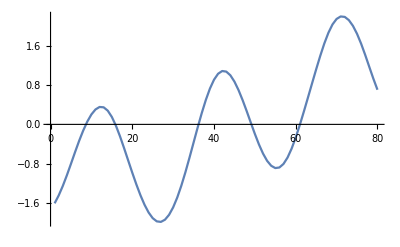

```mathematica
archetypalMeanYes=Mean[Table[reducedOxyYes80[[x,1]],{x,30}]];
ListLinePlot[archetypalMeanYes]
```

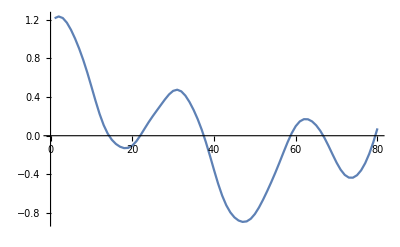

```mathematica
archetypalMeanNo = Mean[Table[reducedOxyNo80[[x,1]],{x,30}]];
ListLinePlot[archetypalMeanNo]
```

### Time to generalize to various metrics

```mathematica
archetypal[f_]:=ListLinePlot[{Legended[f[Table[reducedOxyYes80[[x,1]],{x,30}]],"Oxy Yes"],Legended[f[Table[reducedOxyNo80[[x,1]],{x,30}]],"Oxy No"]},PlotLabel->f]
```

Test on the Mean function:

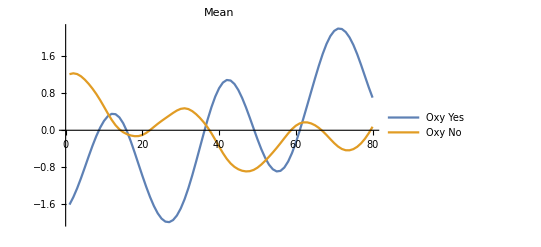

```mathematica
archetypal[Mean]
```

Generation of a list of archetypal based on standard statistical measures:

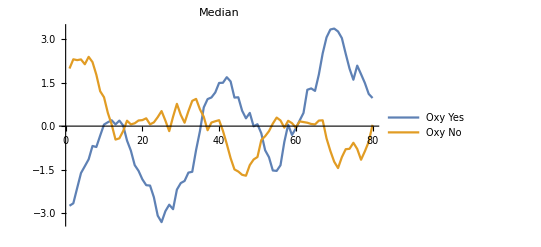
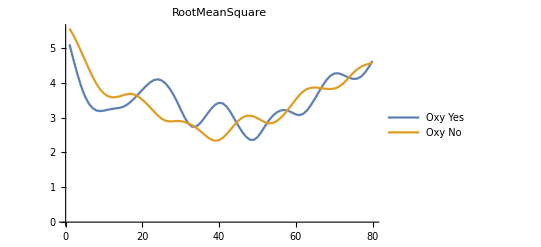
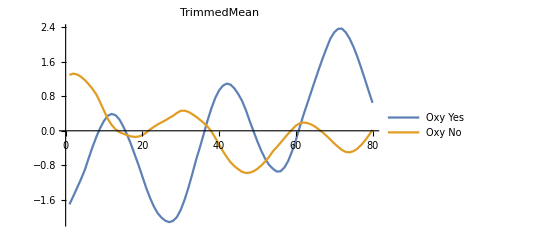
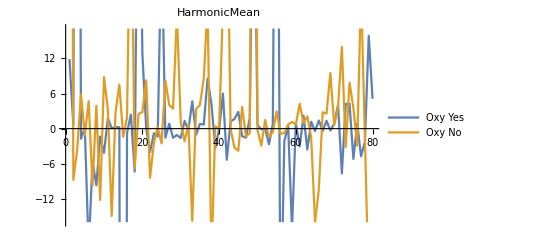
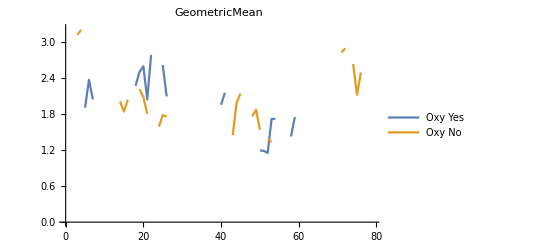
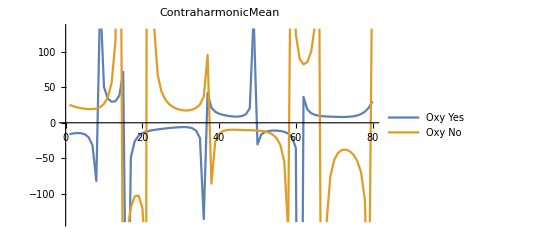
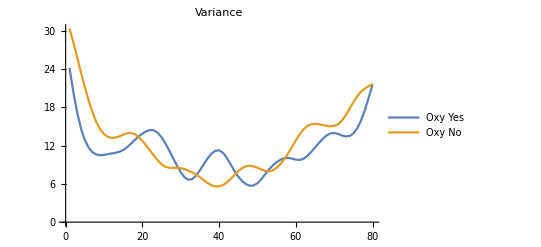
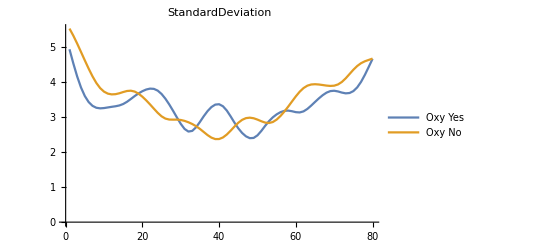
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
energy=Total@(#^2)&;
stats={Mean,Median,RootMeanSquare,TrimmedMean,HarmonicMean,GeometricMean,ContraharmonicMean,Variance,StandardDeviation,MeanDeviation,MedianDeviation,QuartileDeviation,InterquartileRange,Skewness,Kurtosis,QuartileSkewness,Entropy,energy};
Column[Style[archetypal[#],Larger]&/@stats]
```

#### Comment about the above results :

It seems like only the Mean function can give two quite different archetypals

## Experiments with DTW